# L Nl Pet Site

```mathematica
(*Set global parameters*)t=5;
c=2;
W=1;
K=8;
l=t*c;
v=0.173;

(*Shared random onsite potential generator*)
generateG[t_,W_]:=RandomReal[{-t,t}];

(*ml matrix:tridiagonal with random onsite+constant hopping*)
makeML[t_,W_,K_]:=Module[{Ox},
Ox=ConstantArray[0,{K,K}];
Do[Ox[[i,i]]=W,{i,1,K}];
Do[Ox[[i+1,i]]=generateG[t,W];Ox[[i,i+1]]=generateG[t,W],{i,1,K-1}];Ox=(Ox+Transpose[Ox])/2;
Rationalize[Ox,Power[10,-20]]];

(*mnl matrix:exponential decay hopping+random onsite*)
makeMNL[t_,W_,K_,l_,c_]:=Module[{Ox},Ox=Table[generateG[t,W]/c^Abs[i-j],{i,1,K},{j,1,K}];
Ox=(Ox+Transpose[Ox])/2;
Do[Ox[[i,i]]=W,{i,1,K}];
Rationalize[Ox,Power[10,-20]]];

(*mpet matrix:modified Petersen graph adjacency+random onsite+exponential decay*)
makeMPET[t_,W_,K_,l_,c_]:=Module[{mat,p},
p=PetersenGraph[K/2,K/4];
mat=WeightedAdjacencyMatrix[p];
Do[mat[[i,i]]=W,{i,1,K}];
Do[Do[If[i=!=j,mat[[i,j]]=generateG[t,W]*mat[[i,j]]/c^Abs[i-j]],{j,1,K}],{i,1,K}];mat=(mat+Transpose[mat])/2;
Normal[Rationalize[mat,Power[10,-20]]]];
(*Module to compute neutrino masses and mixing matrices*)NeutrinoLocalMass[t_,W_,K_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,Lmix,mass,Rmix,masses,vr,yukr,hamr},vr=Rationalize[v,Power[10,-pr]];hamr =Rationalize[ham,Power[10,-pr]]; 
yukr =Rationalize[yuk,Power[10,-pr]]; ml1=makeML[t,W,K];ml2=makeML[t,W,K];ml3=makeML[t,W,K];ml4=makeML[t,W,K];ml5=makeML[t,W,K];ml6=makeML[t,W,K];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[TotalML,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1]];R2=Rmat[[1+K]];R3=Rmat[[1+2 K]];
Mma=Table[0,{i,1,3 K+3},{j,1,3 K+3}];
i=1;While[i<=3 K,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<=3 K,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]]*yukr[[1,1]]+vr*L2[[i]]*yukr[[1,2]]+vr*L3[[i]]*yukr[[1,3]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L1[[i]]*yukr[[2,1]]+vr*L2[[i]]*yukr[[2,2]]+vr*L3[[i]]*yukr[[2,3]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L1[[i]]*yukr[[3,1]]+vr*L2[[i]]*yukr[[3,2]]+vr*L3[[i]]*yukr[[3,3]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i=1;
While[i<4,{j=1;
While[j<4,{PMNS[[j,-i]]=Lmix[[j,-4+i]]};j++]};
i++] ;
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)NeutrinoNonLocalMass[t_,W_,K_,l_,c_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,Lmix,mass,Rmix,masses,vr,yukr,hamr},vr=Rationalize[v,Power[10,-pr]];hamr =Rationalize[ham,Power[10,-pr]];yukr =Rationalize[yuk,Power[10,-pr]]; ml1=makeMNL[t,W,K,l,c];ml2=makeMNL[t,W,K,l,c];ml3=makeMNL[t,W,K,l,c];ml4=makeMNL[t,W,K,l,c];ml5=makeMNL[t,W,K,l,c];ml6=makeMNL[t,W,K,l,c];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[TotalML,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1]];R2=Rmat[[1+K]];R3=Rmat[[1+2 K]];
Mma=Table[0,{i,1,3 K+3},{j,1,3 K+3}];
i=1;While[i<=3 K,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<=3 K,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]]*yukr[[1,1]]+vr*L2[[i]]*yukr[[1,2]]+vr*L3[[i]]*yukr[[1,3]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L1[[i]]*yukr[[2,1]]+vr*L2[[i]]*yukr[[2,2]]+vr*L3[[i]]*yukr[[2,3]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L1[[i]]*yukr[[3,1]]+vr*L2[[i]]*yukr[[3,2]]+vr*L3[[i]]*yukr[[3,3]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i=1;
While[i<4,{j=1;
While[j<4,{PMNS[[j,-i]]=Lmix[[j,-4+i]]};j++]};
i++] ;
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)NeutrinoPetMass[t_,W_,K_,l_,c_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,Lmix,mass,Rmix,masses,vr,yukr,hamr},vr=Rationalize[v,Power[10,-pr]];hamr =Rationalize[ham,Power[10,-pr]]; 
yukr =Rationalize[yuk,Power[10,-pr]]; ml1=makeMPET[t,W,K,l,c];ml2=makeMPET[t,W,K,l,c];ml3=makeMPET[t,W,K,l,c];ml4=makeMPET[t,W,K,l,c];ml5=makeMPET[t,W,K,l,c];ml6=makeMPET[t,W,K,l,c];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[TotalML,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1]];R2=Rmat[[1+K]];R3=Rmat[[1+2 K]];
Mma=Table[0,{i,1,3 K+3},{j,1,3 K+3}];
i=1;While[i<=3 K,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<=3 K,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]]*yukr[[1,1]]+vr*L2[[i]]*yukr[[1,2]]+vr*L3[[i]]*yukr[[1,3]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L1[[i]]*yukr[[2,1]]+vr*L2[[i]]*yukr[[2,2]]+vr*L3[[i]]*yukr[[2,3]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L1[[i]]*yukr[[3,1]]+vr*L2[[i]]*yukr[[3,2]]+vr*L3[[i]]*yukr[[3,3]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i=1;
While[i<4,{j=1;
While[j<4,{PMNS[[j,-i]]=Lmix[[j,-4+i]]};j++]};
i++] ;
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)NeutrinoLocalMajoranaMass[t_,W_,K_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,i1,j1,Lmix,Ox,Mm2,a1,a2,a3,ac,Mm,ar1,ar2,ar3,Mn,mass,Rmix,masses,PMNS,Mm1,vr,yukr,hamr,Wr},vr=Rationalize[v,Power[10,-pr]];hamr =Rationalize[ham,Power[10,-pr]]; Wr=Rationalize[W,Power[10,-pr]];yukr =Rationalize[yuk,Power[10,-pr]];ml1=makeML[t,W,K];ml2=makeML[t,W,K];ml3=makeML[t,W,K];ml4=makeML[t,W,K];ml5=makeML[t,W,K];ml6=makeML[t,W,K];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
Ox = Table[0,{i,1,3K},{j,1,3K}]; a1 = Table[0,{i,1,2K*3}];
a2 = Table[0,{i,1,2K*3}];
a3 = Table[0,{i,1,2K*3}];
ac = {a1,a2,a3};i=1;
While[i<4,{ac[[i,1+K*(i-1)]]=t};i++];Mm = {{Ox,TotalML},{Transpose[TotalML],Ox}};
Mm1 =ArrayFlatten[Mm];Mm2 = Transpose[Join[Mm1,{ac[[1]]},{ac[[2]]},{ac[[3]]}]];
ar1 = Append[ac[[1]],yukr[[1,1]]*Wr];AppendTo[ar1,yukr[[1,2]]*Wr];AppendTo[ar1,yukr[[1,3]]*Wr];
ar2 = Append[ac[[2]],yukr[[2,1]]*Wr];AppendTo[ar2,yukr[[2,2]]*Wr];AppendTo[ar2,yukr[[2,3]]*Wr];
ar3 = Append[ac[[3]],yukr[[3,1]]*Wr];AppendTo[ar3,yukr[[3,2]]*Wr];AppendTo[ar3,yukr[[3,3]]*Wr];Mn = Join[Mm2,{ar1},{ar2},{ar3}] ;
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[Mn,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1+3*K]];R2=Rmat[[1+K+3*K]];R3=Rmat[[1+2 K+3*K]];
Mma=Table[0,{i,1,6 K+6},{j,1,6 K+6}];
i=1;While[i<2K*3+4,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<2K*3+4,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L2[[i]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L3[[i]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i1=1;
While[i1<4,{j1=1;
While[j1<4,{PMNS[[j1,-i1]]=Lmix[[j1,-4+i1]]};j1++]};
i1++] ;
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)NeutrinoNonLocalMajoranaMass[t_,W_,K_,l_,c_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,i1,j1,Lmix,Ox,Mm2,a1,a2,a3,ac,Mm,ar1,ar2,ar3,Mn,mass,Rmix,masses,PMNS,Mm1,vr,yukr,hamr,Wr},vr=Rationalize[v,Power[10,-pr]];hamr =Rationalize[ham,Power[10,-pr]]; Wr=Rationalize[W,Power[10,-pr]];yukr =Rationalize[yuk,Power[10,-pr]];ml1=makeMNL[t,W,K,l,c];ml2=makeMNL[t,W,K,l,c];ml3=makeMNL[t,W,K,l,c];ml4=makeMNL[t,W,K,l,c];ml5=makeMNL[t,W,K,l,c];ml6=makeMNL[t,W,K,l,c];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
Ox = Table[0,{i,1,3K},{j,1,3K}]; a1 = Table[0,{i,1,2K*3}];
a2 = Table[0,{i,1,2K*3}];
a3 = Table[0,{i,1,2K*3}];
ac = {a1,a2,a3};i=1;
While[i<4,{ac[[i,1+K*(i-1)]]=t};i++];Mm = {{Ox,TotalML},{Transpose[TotalML],Ox}};
Mm1 =ArrayFlatten[Mm];Mm2 = Transpose[Join[Mm1,{ac[[1]]},{ac[[2]]},{ac[[3]]}]];
ar1 = Append[ac[[1]],yukr[[1,1]]*Wr];AppendTo[ar1,yukr[[1,2]]*Wr];AppendTo[ar1,yukr[[1,3]]*Wr];
ar2 = Append[ac[[2]],yukr[[2,1]]*Wr];AppendTo[ar2,yukr[[2,2]]*Wr];AppendTo[ar2,yukr[[2,3]]*Wr];
ar3 = Append[ac[[3]],yukr[[3,1]]*Wr];AppendTo[ar3,yukr[[3,2]]*Wr];AppendTo[ar3,yukr[[3,3]]*Wr];Mn = Join[Mm2,{ar1},{ar2},{ar3}] ;
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[Mn,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1+3*K]];R2=Rmat[[1+K+3*K]];R3=Rmat[[1+2 K+3*K]];
Mma=Table[0,{i,1,6 K+6},{j,1,6 K+6}];
i=1;While[i<2K*3+4,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<2K*3+4,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L2[[i]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L3[[i]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i1=1;
While[i1<4,{j1=1;
While[j1<4,{PMNS[[j1,-i1]]=Lmix[[j1,-4+i1]]};j1++]};
i1++] ;
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)NeutrinoPetMajoranaMass[t_,W_,K_,l_,c_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,i1,j1,Lmix,Ox,Mm2,a1,a2,a3,ac,Mm,ar1,ar2,ar3,Mn,mass,Rmix,masses,PMNS,Mm1,vr,yukr,hamr,Wr},vr=Rationalize[v,Power[10,-pr]];hamr =Rationalize[ham,Power[10,-pr]]; 
Wr=Rationalize[W,Power[10,-pr]];yukr =Rationalize[yuk,Power[10,-pr]];ml1=makeMPET[t,W,K,l,c];ml2=makeMPET[t,W,K,l,c];ml3=makeMPET[t,W,K,l,c];ml4=makeMPET[t,W,K,l,c];ml5=makeMPET[t,W,K,l,c];ml6=makeMPET[t,W,K,l,c];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
Ox = Table[0,{i,1,3K},{j,1,3K}]; a1 = Table[0,{i,1,2K*3}];
a2 = Table[0,{i,1,2K*3}];
a3 = Table[0,{i,1,2K*3}];
ac = {a1,a2,a3};i=1;
While[i<4,{ac[[i,1+K*(i-1)]]=t};i++];Mm = {{Ox,TotalML},{Transpose[TotalML],Ox}};
Mm1 =ArrayFlatten[Mm];Mm2 = Transpose[Join[Mm1,{ac[[1]]},{ac[[2]]},{ac[[3]]}]];
ar1 = Append[ac[[1]],yukr[[1,1]]*Wr];AppendTo[ar1,yukr[[1,2]]*Wr];AppendTo[ar1,yukr[[1,3]]*Wr];
ar2 = Append[ac[[2]],yukr[[2,1]]*Wr];AppendTo[ar2,yukr[[2,2]]*Wr];AppendTo[ar2,yukr[[2,3]]*Wr];
ar3 = Append[ac[[3]],yukr[[3,1]]*Wr];AppendTo[ar3,yukr[[3,2]]*Wr];AppendTo[ar3,yukr[[3,3]]*Wr];Mn = Join[Mm2,{ar1},{ar2},{ar3}] ;
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[Mn,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1+3*K]];R2=Rmat[[1+K+3*K]];R3=Rmat[[1+2 K+3*K]];
Mma=Table[0,{i,1,6 K+6},{j,1,6 K+6}];
i=1;While[i<2K*3+4,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<2K*3+4,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L2[[i]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L3[[i]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i1=1;
While[i1<4,{j1=1;
While[j1<4,{PMNS[[j1,-i1]]=Lmix[[j1,-4+i1]]};j1++]};
i1++] ;
{masses,PMNS}]
```

```mathematica
yukawa = IdentityMatrix[3]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
NeutrinoLocalMass[t,W,K,yukawa,yukawa,v,30]
```

{{6.09304188000137272472203594274,5.20719039382009303751632306227,4.88618301192509982071845692639,4.22478433047208420541719523416,4.09304358063803801131487992332,3.20808166175412504777183899379,2.887032185674595745944347714,2.8144410687414106201417602741,2.36645869946409989311989499708,2.22503265615712409537753031044,2.10098825194724219596682358094,1.792134532606465073623951856,1.77753961412865412038203041841,1.42248008115322687173364487392,1.36394016509904285845015182868,1.01257102023850148504541965129,1.00012507038619476785110262388,0.814544966167200176387690000507,0.639473331772745559482239130194,0.583528541177963468999243993516,0.377598914161684123571449162566,0.256927750471498619991781492039,0.20791934296884132735784220764,0.155751846117617114390083002131,0.000677681643997918456545121238359,0.000139204296432650763026782042363,3.10407548688860436264663112859×10^-6},(1.02243053476267659620651361347×10^-39 | -7.52779984897872459081487968944×10^-41 | -0.955687906016796570009001765918
5.35013708262753414301508248533×10^-43 | -0.994608935456530913910296414238 | -1.36021786492031171608297600319×10^-37
-0.624352437396031826990887370882 | -6.56436399018951934193135677432×10^-43 | -1.60075892725431889272392407094×10^-39)}

```mathematica
ml1=makeML[t,2W,K]//N;
ml2=makeMNL[t,2W,K,l,c]//N;
ml3=makeMPET[t,2W,K,l,c]//N;
```

```mathematica
ec=Eigenvectors[N[ml1]];
ev=Eigenvalues[N[ml1]];
ec2=Eigenvectors[N[ml2]];
ev2=Eigenvalues[N[ml2]];
ec3=Eigenvectors[N[ml3]];
ev3=Eigenvalues[N[ml3]];
```

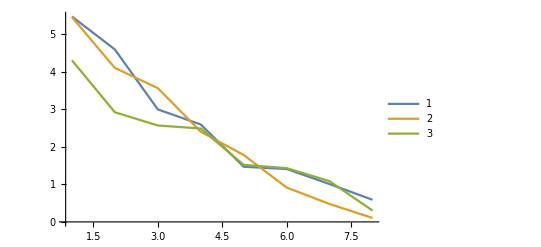

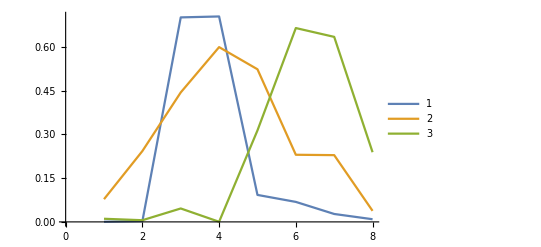

```mathematica
ListLinePlot[Abs[{ev,ev2,ev3}],PlotRange->All,PlotLegends->Automatic]
ListLinePlot[Abs[{ec[[1]],ec2[[1]],ec3[[1]]}],PlotLegends->Automatic]
```